```mathematica
With[{νr = 462, νg = 545, νb = 666}, Table[RGBColor@N[#/Max[#]&@{(1/ν)^3/(Exp[νr/ν] - 1), (1/ν)^3/(Exp[νg/ν] - 1), (1.7(1/ν)^3)/(Exp[νb/ν] - 1)}], {ν, 430, 700, 20}]]
```

{RGBColor[{1., 0.755672028334821, 0.8845378707999877}],RGBColor[{1., 0.7601114670419287, 0.8977348664503951}],RGBColor[{1., 0.7641519602242668, 0.9098419203026309}],RGBColor[{1., 0.7678439650173209, 0.9209842592102772}],RGBColor[{1., 0.7712299116519472, 0.9312692705870258}],RGBColor[{1., 0.7743457155361246, 0.9407894566102927}],RGBColor[{1., 0.777221964461637, 0.9496248442474693}],RGBColor[{1., 0.7798848585427864, 0.9578449586093919}],RGBColor[{1., 0.7823569602582787, 0.9655104452261531}],RGBColor[{1., 0.7846577974110117, 0.9726744092765065}],RGBColor[{1., 0.7868043512465959, 0.9793835258550571}],RGBColor[{1., 0.7888114542180275, 0.9856789643405852}],RGBColor[{1., 0.7906921161473742, 0.9915971612375593}],RGBColor[{1., 0.7924577932543819, 0.9971704690089769}]}

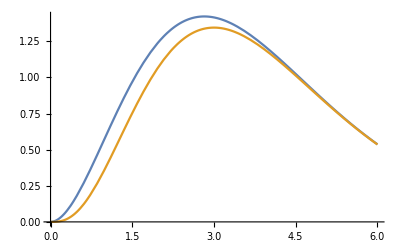

```mathematica
Plot[{x^3/(Exp[x] - 1), x^3/Exp[x]}, {x, 0, 6}]
```

```mathematica
D[x^3/(Exp[x] - 1), {x, 2}] // Simplify
```

(x (6+ⅇ^(2 x) (6-6 x+x^2)+ⅇ^x (-12+6 x+x^2)))/((-1+ⅇ^x)^3)

```mathematica
D[x^3/(Exp[x] - 1), {x, 4}] // Simplify
```

(ⅇ^x (24+36 x+12 x^2+x^3+ⅇ^(3 x) (-24+36 x-12 x^2+x^3)+ⅇ^(2 x) (72-36 x-36 x^2+11 x^3)+ⅇ^x (-72-36 x+36 x^2+11 x^3)))/((-1+ⅇ^x)^5)

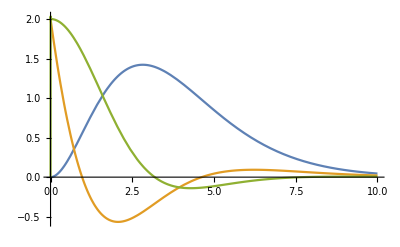

```mathematica
Plot[{x^3/(Exp[x] - 1), (x (6+ⅇ^(2 x) (6-6 x+x^2)+ⅇ^x (-12+6 x+x^2)))/((-1+ⅇ^x)^3), (ⅇ^x (24+36 x+12 x^2+x^3+ⅇ^(3 x) (-24+36 x-12 x^2+x^3)+ⅇ^(2 x) (72-36 x-36 x^2+11 x^3)+ⅇ^x (-72-36 x+36 x^2+11 x^3)))/((-1+ⅇ^x)^5)}, {x, 0, 10}]
```

```mathematica
D[x^3/Exp[x], {x, 2}] // Simplify
```

ⅇ^-x x (6-6 x+x^2)

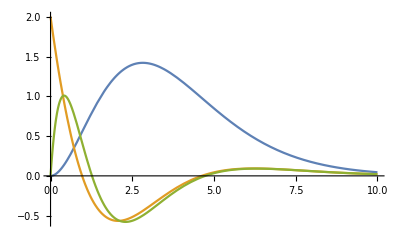

```mathematica
Plot[{x^3/(Exp[x] - 1), (x (6+ⅇ^(2 x) (6-6 x+x^2)+ⅇ^x (-12+6 x+x^2)))/((-1+ⅇ^x)^3), ⅇ^-x x (6-6 x+x^2)}, {x, 0, 10}]
```

```mathematica
Exp[2.82]
```

16.7769

```mathematica
NSolve[Exp[-x] == 1 - x/3, x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.},{x→2.82144}}

```mathematica
Integrate[x^3/Exp[x] Exp[-(x - x0)^2], {x, 0, ∞}]
```

1/16 ⅇ^(-x0^2) (10+8 (-1+x0) x0+ⅇ^((-1/2+x0)^2) √π (-1+2 x0) (7+4 (-1+x0) x0) Erfc[1/2-x0])

```mathematica
Integrate[x^3/Exp[x] Exp[-(x - x0)^2], {x, -∞, ∞}]
```

1/8 ⅇ^(1/4-x0) √π (-1+2 x0) (7+4 (-1+x0) x0)

```mathematica
Simplify[Integrate[(ν/νn)^3/Exp[ν/νn] Exp[-(ν - ν0)^2/(4 σ^2)], {ν, -∞, ∞}, Assumptions -> {σ > 0, νn > 0, ν0 > 0}], Assumptions -> {σ > 0, νn > 0, ν0 > 0}]
```

(2 ⅇ^((-ν0 νn+σ^2)/νn^2) √π σ (ν0 νn-2 σ^2) (ν0^2 νn^2+2 νn (-2 ν0+3 νn) σ^2+4 σ^4))/νn^6

```mathematica
Simplify[Integrate[(ν/νn)^3/Exp[ν/νn] Exp[-(ν - ν0)^2/(2 σ^2)], {ν, 0, ∞}, Assumptions -> {σ > 0, νn > 0, ν0 > 0}], Assumptions -> {σ > 0, νn > 0, ν0 > 0}]
```

1/(2 νn^6)ⅇ^(-ν0^2/(2 σ^2)) σ (2 νn σ (ν0^2 νn^2-2 ν0 νn σ^2+2 νn^2 σ^2+σ^4)+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2))+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2)) Erf[(ν0 νn-σ^2)/(√2 νn σ)])

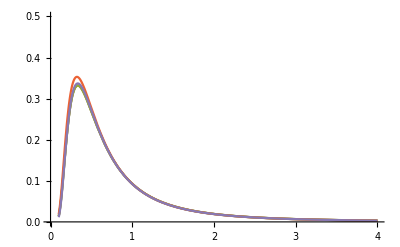

```mathematica
With[{σ = 0.1, ν0 = 1}, Plot[{1/(2 νn^6)ⅇ^(-ν0^2/(2 σ^2)) σ (2 νn σ (ν0^2 νn^2-2 ν0 νn σ^2+2 νn^2 σ^2+σ^4)+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2))+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2)) Erf[(ν0 νn-σ^2)/(√2 νn σ)]), (√(2 π))/νn^6 ⅇ^(-ν0^2/(2 σ^2)) σ (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2))ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2), √(2π) σ ⅇ^(-(ν0^2 - (ν0 - σ^2/νn)^2)/(2 σ^2)) ((ν0^3 + 3ν0 σ^2)/νn^3 - (3 ν0^2 σ^2 + 3 σ^4)/νn^4 + (3ν0 σ^4)/νn^5 - (3 σ^6)/νn^6), √(2π) σ ⅇ^(-(ν0^2 - (ν0 - σ^2/νn)^2)/(2 σ^2)) ν0^3/νn^3, √(2π) σ ⅇ^(-ν0/νn) ν0^3/νn^3}, {νn, 0.1, 4}, PlotRange -> {0, 0.5}]]
```

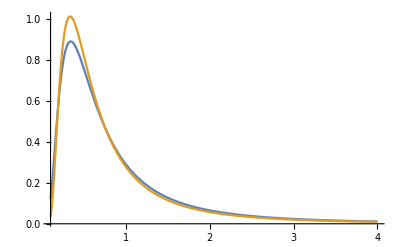

```mathematica
With[{σ = 0.3, ν0 = 1}, Plot[{1/(2 νn^6)ⅇ^(-ν0^2/(2 σ^2)) σ (2 νn σ (ν0^2 νn^2-2 ν0 νn σ^2+2 νn^2 σ^2+σ^4)+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2))+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2)) Erf[(ν0 νn-σ^2)/(√2 νn σ)]), √(2π) σ ⅇ^(-ν0/νn) ν0^3/νn^3}, {νn, 0.1, 4}, PlotRange -> All]]
```

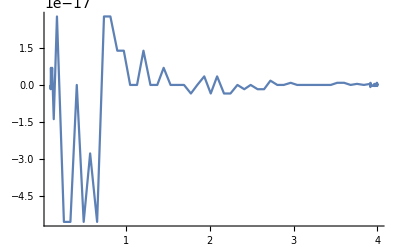

```mathematica
With[{σ = 0.1, ν0 = 1}, Plot[1/(2 νn^6)ⅇ^(-ν0^2/(2 σ^2)) σ (2 νn σ (ν0^2 νn^2-2 ν0 νn σ^2+2 νn^2 σ^2+σ^4)+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2))+ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2) √(2 π) (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2)) Erf[(ν0 νn-σ^2)/(√2 νn σ)]) - (√(2 π))/νn^6 ⅇ^(-ν0^2/(2 σ^2)) σ (ν0^3 νn^3-3 ν0^2 νn^2 σ^2+3 ν0 νn σ^2 (νn^2+σ^2)-σ^4 (3 νn^2+σ^2))ⅇ^(1/2 (1/νn-ν0/σ^2)^2 σ^2), {νn, 0.1, 4}, PlotRange -> All]]
```